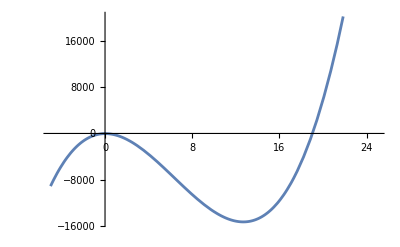

```mathematica
(*
ЗАДАНИЕ 1
Отделите графически корни алгебраического уравнения f (x)=0 с помощью функ-ции Plot.
Найдите один из них (нецелый) с точностью ε=10^(−3) методом хорд.Укажите
потребовавшееся число итераций.Проиллюстрируйте графически нахождение первых
двух приближений (постройте график функции и хорды).
1.1.f(x)=15x^3−86x^2+11x−28.
*)
f[x_]:=15 x^3-286x^2+11 x-28
Plot[f[x],{x,-5,25}]
```

```mathematica
chordMethod[f_,a_,b_,eps_]:=Module[{x0=a,x1=b,x2,ll,iter=0,history={}},
While[True,x2=x1-f[x1]*(x1-x0)/(f[x1]-f[x0]);
iter++;
ll = (x2-x1)^2/Abs[x2+x0-2*x1];
AppendTo[history,{iter,N[x2,6],N[f[x2],6],N[ll,6]}];
If[ll<eps,Break[]];
x0=x1;
x1=x2;];
{N[x2,6],iter,history}]
```

Найденный корень: 19.0333

Потребовавшееся число итераций: 4

Таблица итераций:

№ | x_n | f(x_n) | ll
1 | 18.7561 | -1460.27 | 1.45262
2 | 18.9624 | -381.976 | 0.0123262
3 | 19.0354 | 11.5329 | 0.0400732
4 | 19.0333 | -0.0864541 | 0.0000609603

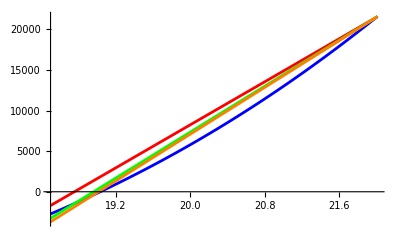

Найденный корень: 3.66664

Потребовавшееся число итераций: 5

Таблица итераций:

1 | 3.41892 | -37.9942 | 0.21356
2 | 3.59697 | -12.7427 | 0.0417624
3 | 3.68682 | 4.00309 | 0.0915319
4 | 3.66535 | -0.257251 | 0.00414399
5 | 3.66664 | -0.00465082 | 0.

```mathematica
result=chordMethod[f,18,22,10^-3];
Print["Найденный корень: ",result[[1]]];
Print["Потребовавшееся число итераций: ",result[[2]]];
Print["Таблица итераций:"];
Print[TableForm[result[[3]],TableHeadings->{None,{"№","x_n","f(x_n)","ll"}}]];


chord[x_,a_,b_]:=f[a]+(f[b]-f[a])/(b-a)*(x-a)
chord1[x_]:=chord[x,18,22];
chord2[x_]:=chord[x,result[[3,1,2]],22];
chord3[x_]:=chord[x,result[[3,2,2]],22];

Plot[{f[x],chord1[x],chord2[x],chord3[x]},{x,18.5,22.01},PlotStyle->{Blue,Red,Green,Orange}]
```

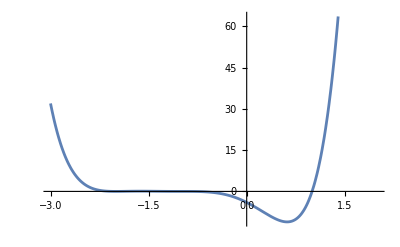

```mathematica
(*
ЗАДАНИЕ 2: 
Отделите графически и найдите с помощью функций Solve,NSolve,Roots,FindRoot
корни алгебраического уравнения f(x)=0. Разложите многочлен f (x) на множители, используя функцию Factor.
2.1.f (x)=x^6+6x^5+12x^4+6x^3−9x^2−12x−4.
*)
f2[x_]:=x^6+6x^5+12x^4+6x^3-9x^2-12x-4;
Plot[f2[x],{x,-3,2}]
```

```mathematica
Solve[f2[x]==0, x]
NSolve[f2[x]==0, x]
Roots[f2[x] ==0, x]
FindRoot[f2[x]==0,{x,-1.8}]
```

{{x→-2},{x→-2},{x→-1},{x→-1},{x→-1},{x→1}}

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

x==-2||x==-2||x==-1||x==-1||x==-1||x==1

{x→-2.}

```mathematica
Factor[f2[x]]
```

(-1+x) (1+x)^3 (2+x)^2

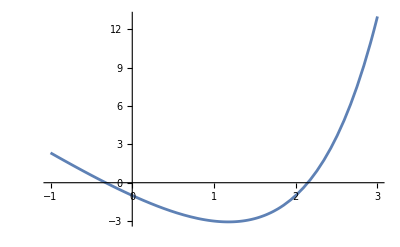

```mathematica
(*
3. Отделите графически корни трансцендентного уравнения с помощью функции Plot.
Найдите один из них с точностью ε=10^(−3):
а) методом Ньютона;
	б) методом секущих.
	Укажите потребовавшееся число итераций.
3.1.3^x=4x+2.
*)
f3[x_]:=3^(x)-4x-2;
Plot[f3[x],{x,-1,3}]
```

```mathematica
df3[x_]:=f3'[x];
d2f3[x_] := df3'[x];
newtonMethod[f_,a_,eps_] = Module[{x1=a,x2,iter=0, history={}} ,
while[True, x2 = x1-f3[x1]/df3[x1];
iter++;
AppendTo[history,{iter,N[x2,6],N[f[x2],6]}];
If[f3[x2]<eps, Break[]];
x1=x2;
 ];
{N[x2,6],iter,history}]
(*Этим методом будем искать корень находящийся в промежутке (-1,0)*)
```

{-(1. (-2.+3.^a-4. a))/(-4.+1.09861 3.^a)+a,1,{{1,-(1. (-2.+3.^a-4. a))/(-4.+1.09861 3.^a)+a,-28.+11. (-(1. (-2.+3.^a-4. a))/(-4.+1.09861 3.^a)+a)-286. (-(1. (-2.+3.^a-4. a))/(-4.+1.09861 3.^a)+a)^2+15. (-(1. (-2.+3.^a-4. a))/(-4.+1.09861 3.^a)+a)^3}}}

```mathematica
N[f3[-1]*d2f3[-1],6]
N[f3[0]*d2f3[0],6]
```

0.938738

-1.20695

-1.20695

0.938738